# (Progress (Report))^2

## Reese Danzer and Karthik Boyareddygari

## I - User Manual

Step 1: Open “Main.nb”
Step 2: Scroll down to and evaluate the “interface[]” cell--as well as the initilization cells.
Step 3: Program is functional and interactive.

## II and III

## IV - Formulas

### Interpolation Across Datasets

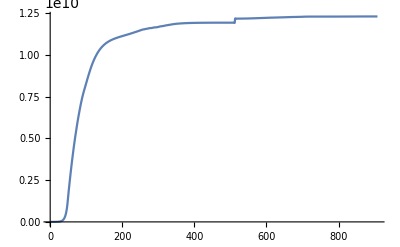
Our goal is to create a display that shows a star as a function of time. Our data sets possess a column with the age of the star, and sadly, the values for the age of the star are not lineraly distributed across every row of the dataset. As you can see from this graph of Row Number vs. Age (sorry its not labeled!) there are large gaps of time at the start of the dataset, and and a 2 million year jump in time towards the end:

-Graphics-
What this means is that we have to use age as our manipulate value, and we won’t be able to get away with using the row numbers in manipulate. This does pose somewhat of a problem, as row numbers are one of the key ways two dimensional data stores are organized, and are kind of a baseline necessity for most data functions. Add that to the fact that we’re attempting to create a continuous timeline and have to interpolate a lot, and we have a fairly major challenge.

To fix this we’ve written a function that will, once we finish it up, take the parameters of age, a quantity, and a function (generally intended to be the inverse of the function of row number vs age graphed above) and use the input age to determine the approprate row value and then interpolate the specified quantity from said row value. It is however, a work in progress, and we are considering alternative methods of solving this problem that may be more efficient.

## V - Files

### Star Data

## VI - Data Organization

### Datasets

## VII - Overview

## VIII - Accomplishments